```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_8"];

LNDatabeta095=ReadList["LNData_NM_beta_0.95.txt"];
LNDatabeta096=ReadList["LNData_NM_beta_0.96.txt"];
LNDatabeta097=ReadList["LNData_NM_beta_0.97.txt"];
LNDatabeta098=ReadList["LNData_NM_beta_0.98.txt"];
LNDatabeta099=ReadList["LNData_NM_beta_0.99.txt"];
LNDatabeta100=ReadList["LNData_NM_beta_1.txt"];
LNDatabeta101=ReadList["LNData_NM_beta_1.01.txt"];
LNDatabeta102=ReadList["LNData_NM_beta_1.02.txt"];
LNDatabeta103=ReadList["LNData_NM_beta_1.03.txt"];
LNDatabeta104=ReadList["LNData_NM_beta_1.04.txt"];
LNDatabeta105=ReadList["LNData_NM_beta_1.05.txt"];
```

```mathematica
MeanBetaData={
{0.95, Mean[Table[LNDatabeta095[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.96, Mean[Table[LNDatabeta096[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.97, Mean[Table[LNDatabeta097[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.98, Mean[Table[LNDatabeta098[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.99, Mean[Table[LNDatabeta099[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.00, Mean[Table[LNDatabeta100[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.01, Mean[Table[LNDatabeta101[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.02, Mean[Table[LNDatabeta102[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.03, Mean[Table[LNDatabeta103[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.04, Mean[Table[LNDatabeta104[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.05, Mean[Table[LNDatabeta105[[1]][[pt]][[2]], {pt, 100, 1001}]]}
};
```

```mathematica
(* LN12 and LN34 Data *)
LNBetaData={
{LNDatabeta095[[1]], LNDatabeta095[[6]], 0.95},
{LNDatabeta096[[1]], LNDatabeta096[[6]], 0.96},
{LNDatabeta097[[1]], LNDatabeta097[[6]], 0.97},
{LNDatabeta098[[1]], LNDatabeta098[[6]], 0.98},
{LNDatabeta099[[1]], LNDatabeta099[[6]], 0.99},
{LNDatabeta100[[1]], LNDatabeta100[[6]], 1.00},
{LNDatabeta101[[1]], LNDatabeta101[[6]], 1.01},
{LNDatabeta102[[1]], LNDatabeta102[[6]], 1.02},
{LNDatabeta103[[1]], LNDatabeta103[[6]], 1.03},
{LNDatabeta104[[1]], LNDatabeta104[[6]], 1.04},
{LNDatabeta105[[1]], LNDatabeta105[[6]], 1.05}
};
```

```mathematica
(* Plotting Properties *)
width=600;
height=300;
PlotFormat1={LabelStyle->Directive[18], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
LabelingInfo1={AxesLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, β, η=0, m=1, ω=8, Ω=8, γ=0.5"};
LabelingInfo2={AxesLabel->{"τ", "ℒ𝒩"}};
```

```mathematica
(* LN12 and LN34 Plot as a function of β *)
LNBetaPlots=Table[ListPlot[{LNBetaData[[betavalue]][[1]], LNBetaData[[betavalue]][[2]]}, Joined->True, Evaluate[PlotFormat1], Evaluate[LabelingInfo2], PlotLabel->"n=4, β="<>ToString[LNBetaData[[betavalue]][[3]]]<>", η=0, m=1, ω=8, Ω=8, γ=0.5}"], {betavalue, 1, Length[LNBetaData]}];
ListAnimate[LNBetaPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

InterpolatingFunction[…]

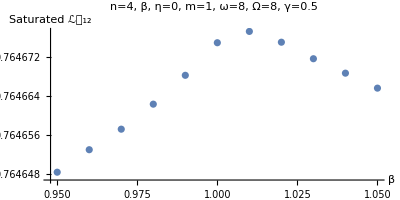
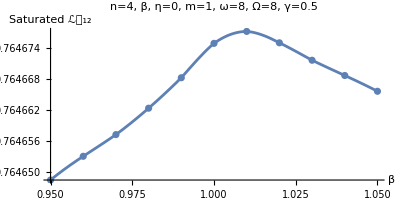

```mathematica
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Interpolation: Must zoom in to where the suspected maximum is. *)
iMeanBetafunc=Interpolation[MeanBetaData]
iMeanBetaDatalinePlot=Plot[iMeanBetafunc[x], {x, 0.95, 1.05}, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show together *)
Row[{MeanBetaDataptPlotZoom, Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom]}]
```

```mathematica
(* Take the derivative of the Interpolation Function *)
derivfunc[β_]:=D[iMeanBetafunc[x], x]/.x->β
(* Calculating the value of the derivative of Interpolation Function near the maximum. Get start and end values from the graph. *)
start= 1.00;
end=1.02;
deridata=Table[{β, derivfunc[β]}, {β, start, end, 10^-6}];
```

{1.01,0.764677}

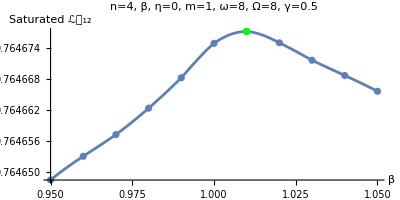

```mathematica
(* Finding Optimum β for when Ω=ω=6 *)
βmax={};
Table[If[deridata[[value]][[2]]>0 && deridata[[value+1]][[2]]<0, AppendTo[βmax, Mean[{deridata[[value]][[1]],deridata[[value+1]][[1]]}]]], {value, 1, Length[deridata]-1}];
optimumpt=Flatten[{βmax, iMeanBetafunc[βmax]}]
(* Plot {βmax, Saturated LN12} *)
optimumptPlot=ListPlot[{optimumpt}, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotStyle->Green];
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom, optimumptPlot]
```

```mathematica
iLfunc=NonlinearModelFit[LNBetaData[[6]][[1]], c/(1+a*Exp[b*x]), {a, b, c}, x]
iLfuncPlot=Plot[iLfunc[x], {x, 0, 500}, PlotRange->{{0, 40}, {0, 0.8}}, PlotStyle->Directive[Dashed, Blue]];
```

FittedModel[…]

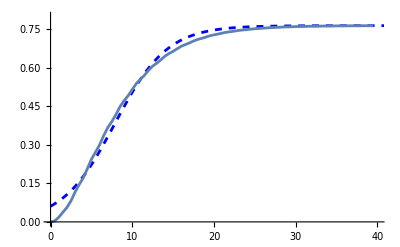

```mathematica
Show[{iLfuncPlot, ListPlot[{LNBetaData[[6]][[1]][[1;;80]]}, Joined->True]}]
```

FittedModel[…]

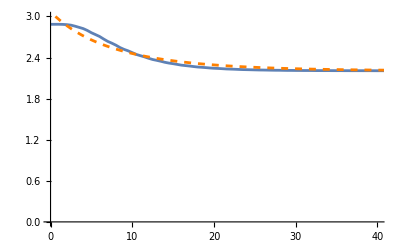

```mathematica
iLfunc2=NonlinearModelFit[LNBetaData[[6]][[2]], c/(1+a*Exp[b*x]), {a, b, c}, x]
iLfuncPlot2=Plot[iLfunc2[x], {x, 0, 500}, PlotRange->{{0, 40}, {0, 3}}, PlotStyle->Directive[Dashed, Orange]];

Show[{ListPlot[LNBetaData[[6]][[2]], Joined->True, PlotRange->{{0, 40}, {0, 3}}], iLfuncPlot2}]
```

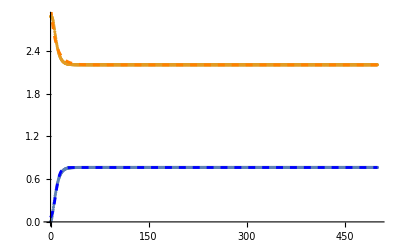

```mathematica
Show[{ListPlot[{LNBetaData[[6]][[1]], LNBetaData[[6]][[2]]}], iLfuncPlot, iLfuncPlot2}]
```